```mathematica
sol = DSolve[{y'[ x]==-4 R  y[x]-g[x]+2/Pi, g'[x]==-16 R  g[x] + 2  y[x], y[0]==2/Pi, g[0]==2/Pi}, {y,g}, x]
```

{{g→Function[{x},1/(π (-1+18 R^2) (1+32 R^2))ⅇ^(-((-10 R+√2 √(-1+18 R^2)) x)) (-ⅇ^((-10 R+√2 √(-1+18 R^2)) x)-ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x)+18 ⅇ^((-10 R+√2 √(-1+18 R^2)) x) R^2-32 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^2+18 ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x) R^2-32 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^2+576 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^4+576 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^4+√2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) √(-1+18 R^2)-√2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) √(-1+18 R^2)+5 √2 ⅇ^((-10 R+√2 √(-1+18 R^2)) x) R √(-1+18 R^2)-8 √2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R √(-1+18 R^2)-5 √2 ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x) R √(-1+18 R^2)+8 √2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R √(-1+18 R^2)+32 √2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^2 √(-1+18 R^2)-32 √2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^2 √(-1+18 R^2)-96 √2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^3 √(-1+18 R^2)+96 √2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^3 √(-1+18 R^2))],y→Function[{x},1/(2 π (-1+18 R^2) (1+32 R^2))ⅇ^(-((-10 R+√2 √(-1+18 R^2)) x)) (-2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x)-2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x)-16 ⅇ^((-10 R+√2 √(-1+18 R^2)) x) R+16 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R-16 ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x) R+16 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R-28 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^2-28 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^2+288 ⅇ^((-10 R+√2 √(-1+18 R^2)) x) R^3-288 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^3+288 ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x) R^3-288 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^3+1152 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^4+1152 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^4-√2 ⅇ^((-10 R+√2 √(-1+18 R^2)) x) √(-1+18 R^2)+√2 ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x) √(-1+18 R^2)+6 √2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R √(-1+18 R^2)-6 √2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R √(-1+18 R^2)+48 √2 ⅇ^((-10 R+√2 √(-1+18 R^2)) x) R^2 √(-1+18 R^2)-80 √2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^2 √(-1+18 R^2)-48 √2 ⅇ^(2 √2 √(-1+18 R^2) x+(-10 R-√2 √(-1+18 R^2)) x) R^2 √(-1+18 R^2)+80 √2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^2 √(-1+18 R^2)+192 √2 ⅇ^(2 (-10 R+√2 √(-1+18 R^2)) x) R^3 √(-1+18 R^2)-192 √2 ⅇ^((-10 R-√2 √(-1+18 R^2)) x+(-10 R+√2 √(-1+18 R^2)) x) R^3 √(-1+18 R^2))]}}

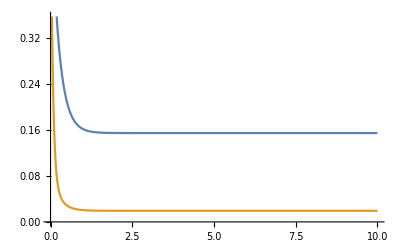

```mathematica
Plot[Evaluate[Table[{y[x],g[x]}/. sol,{R,1}]],{x,0,10}]
```

```mathematica
x
```

x